```mathematica
data={ 
{1, 0.000100, 21315},{1,0.000316,21488},{1,0.001000,22445},{1,0.003162,24757},{1,0.010000,31098},{1,0.031623,44779},{1,0.100000,66560},{1,0.316228,95707},

{0.3,0.000100,21327},{0.3,0.000316,22002},{0.3,0.001000,22877},{0.3,0.003162,24716},{0.3,0.010000,31422},{0.3,0.031623,46019},{0.3,0.100000,66778},{0.3,0.316228,91832},

{0.1,0.000100, 21789},{0.1,0.000316,21755},{0.1,0.001000,23081},{0.1, 0.003162, 25652},{0.1,0.010000,32360},{0.1,0.031623,46972},{0.1,0.100000, 66102},{0.1, 0.316228, 89703},

{0.03,0.000100,23243}, {0.03,0.000316,23311},{0.03,0.001000,24588},{0.03,0.003162,28051},{0.03,0.010000,35365},{0.03,0.031623,50907},{0.03,0.100000,69773},{0.03,0.316228,88225}, 

{0.01,0.000100,26433},{0.01,0.000316,27034} ,{0.01,0.001000,28782},{0.01, 0.003162,32721},{0.01,0.010000, 43412},{0.01,0.031623, 60811},{0.01,0.100000,79280},{0.01,0.316228, 91666} , 

{0.003, 0.000100,36723}, {0.003,0.000316, 37660},{0.003,0.001000,40304},{0.003,0.003162,47950},{0.003,0.010000,62932},{0.003,0.031623, 82956},
{0.003,0.100000, 99946},{0.003,0.316228, 105504},

{0.001,0.000100, 52698},{0.001, 0.000316, 54649},{0.001,0.001000,58392},{0.001,0.003162, 69466},{0.001,0.010000, 89310},{0.001,0.031623,107352},{0.001,0.100000,117308},{0.001,0.316228,122283},

{0.0001, 0.000100,89372}, {0.0001, 0.000316,91890}, {0.0001, 0.001000,95243},{0.0001, 0.003162,106686},{0.0001, 0.010000,122167},{0.0001, 0.031623,131218},{0.0001, 0.100000, 135106}, {0.0001, 0.316228, 138588},

 {0.000100, 0.5, 138952}, {0.000316, 0.5, 135874},{0.001000,0.5, 121273}, {0.003162, 0.5, 107957},{0.010000, 0.5, 93385},
{0.031623, 0.5, 93859}, {0.100000, 0.5, 101611}, {0.316228,0.5,107354}, {1.000000,0.5, 114055}

};


{0.0003, 0.500000, 130725},{0.003,0.500000, 102032},
{0.03,0.500000, 109395},{0.3, 0.500000, 137544},{0.0001, 0.500000,137456}, {0.001, 0.500000, 115161}, {0.01, 0.500000,97497},{0.1, 0.500000, 124388}, {1, 0.500000, 150005}
```

73

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

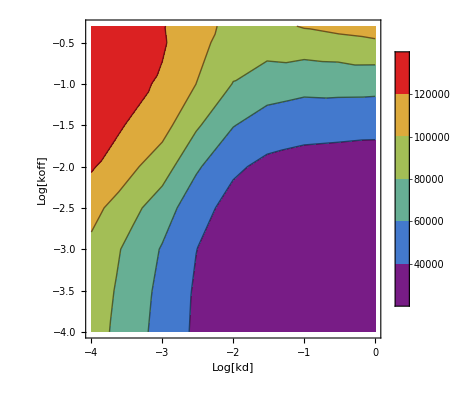

```mathematica
pdata=ListContourPlot[data, InterpolationOrder->3, ColorFunction->"Rainbow"];
Length[data]

ticks=FrameTicks/.AbsoluteOptions[pdata,FrameTicks];

logticks=Apply[If[#1==0,{#1, ,##3},{Log[10,#1],##2}]&,ticks,{2}];

ListContourPlot[{Log[10,#1],Log[10,#2],#3}&@@@data,Mesh->None,PlotRange->All,InterpolationOrder->3,FrameTicks->logticks,ColorFunction->"Rainbow", PlotLegends->Automatic, FrameLabel->{"Log[kd]", "Log[koff]"}]
```